```mathematica
Quit[]
```

```mathematica
Block[{ReadProtected=Sequence[]},
SetDirectory["/home/karl/.Mathematica/Applications/X"];
<<X`;
Names["X`*"];
];
```

Package-X v2.0.3, by Hiren H. Patel

Set::write: Tag X`Utilities`TensorStructures in X`Utilities`TensorStructures[expr_] is Protected.

SetDelayed::write: Tag X`Utilities`CollectByTensorStructures in X`Utilities`CollectByTensorStructures[expr_, f_] is Protected.

For more information, see the

```mathematica
SetDirectory["/home/karl/.Mathematica/Applications/X"]
<<X`
Names["X`*"]
?LoopRefine
```

/home/karl/.Mathematica/Applications/X

Package-X v2.0.3, by Hiren H. Patel

For more information, see the

{C0Expand,ChiralBasis,ChisholmExpand,ContinuedDiLog,Contract,D0Expand,DiLog,DiracAlgebra,DiracMatrix,DiscB,DiscExpand,ExplicitC0,FermionLine,FermionLineExpand,FermionLineProduct,GordonIdentity,IRDivergent,KallenExpand,Kallenλ,KibbleExpand,Kibbleϕ,LDot,Ln,Longitudinal,LoopIntegrate,LoopRefine,LoopRefineSeries,LScalarQ,LTensor,MandelstamRelations,Organization,Projector,PVA,PVB,PVC,PVD,PVX,ScalarC0,ScalarC0IR6,ScalarD0,ScalarD0IR12,ScalarD0IR13,ScalarD0IR16,Spur,TargetScale,Transverse,UVDivergent,𝒹,𝓊,𝓋,𝕘,ℙL,ℙR,γ,γ5,ϵ,ε,σ,$DiracAlgebra,𝟙,µ}

expr converts the "Passarino-Veltman" coefficient functions in \*StyleBox["expr","TI"] to analytic expressions that can be numerically evaluated.

```mathematica
DownValues[ChisholmExpand]
```

{}

```mathematica
DownValues@ChiralBasis
```

{}

```mathematica
ClearAttributes[ChisholmExpand,ReadProtected]
```

```mathematica
Spur[DiracMatrix[Subscript[γ, μ],(l-p).γ+M 𝟙,Subscript[γ, ν],l.γ+M 𝟙]]
int=LoopIntegrate[Spur[DiracMatrix[Subscript[γ, μ],(l-p).γ+M 𝟙,Subscript[γ, ν],l.γ+M 𝟙]],l,-p,M,M]/.{p.p->0}
```

8 l_μ l_ν-4 l_ν p_μ-4 l_μ p_ν+4 M^2 𝕘_(μ,ν)-4 l.l 𝕘_(μ,ν)+4 l.p 𝕘_(μ,ν)

p_μ p_ν (8 PVB[0,1,0,M,M]+8 PVB[0,2,0,M,M])+𝕘_(μ,ν) (-4 PVA[0,M]+8 PVB[1,0,0,M,M])

```mathematica
sol=LoopRefine[int]//DiscExpand
Series[sol,{M,0,2}]
Series[Log[1+h],{h,0,4}]
```

-4/3 (1/ϵ+Log[µ^2/M^2]) p_μ p_ν

-4/3 ((1/ϵ-2 Log[M]+Log[µ^2]) p_μ p_ν)+O[M]^3

h-h^2/2+h^3/3-h^4/4+O[h]^5

```mathematica
Eigenvalues[{{0,m},{m,M}}]
```

{1/2 (M-√(4 m^2+M^2)),1/2 (M+√(4 m^2+M^2))}

```mathematica
Sqrt[D[pot3[r,M,G,a,b,z,rho0,Rs,c],r]*r]
```

√(r (-(4 G π rho0 Rs^2)/(r (1+r/Rs))+(G M r)/((r^2+(a+√(b^2+z^2))^2)^(3/2))+(4 G π rho0 Rs^3 Log[1+r/Rs])/r^2))

```mathematica
pot[r_,M_,G_,a_,b_,z_]:=-(G M)/(r^2+(a+Sqrt[b^2+z^2])^2)^(1/2)
pot2[r_,M_,G_,a_,b_,z_,MDM_,R_]:=-(G M)/(r^2+(a+Sqrt[b^2+z^2])^2)^(1/2)-G MDM (3 R^2 - r^2)/(2 R^3)
pot3[r_,M_,G_,a_,b_,z_,rho0_,Rs_,c_]:=-(G M)/(r^2+(a+Sqrt[b^2+z^2])^2)^(1/2)-4 Pi G rho0( Rs^3 Log[1+r/Rs]/r)
```

```mathematica
velocity=Sqrt[D[pot[r,M,1.,1.,0.5,0.],r]*r]
velocity2=Sqrt[D[pot2[r,M,1.,1.,0.5,0.,5,20],r]*r]
velocity3=Sqrt[D[pot3[r,M,1.,1.,0.5,0.,0.00005,40,5],r]*r]
4 *Pi* 0.00005 20^3(Log[(20 + 5*20)/20]-(5*20)/(20 + 5*20))
```

1. √((M r^2)/((2.25+r^2)^(3/2)))

√(r (0.000625 r+(1. M r)/((2.25+r^2)^(3/2))))

√(r (-1.00531/((1+r/40) r)+(1. M r)/((2.25+r^2)^(3/2))+(40.2124 Log[1+r/40])/r^2))

4.81758

```mathematica
Rasterize[Plot[{velocity/.{M->1.},velocity2/.{M->1.},velocity3/.{M->1.}},{r,0,20},AxesLabel->{r,"Rotational velocity"},PlotLegends->Placed[{"No dark matter", "Spherical uniform halo", "Spherical NFW halo"},Below]],ImageResolution->200]
```

-Graphics-

```mathematica
D[pot3[r,M,G,a,b,z,rho0,Rs,c],r]*r
```

r ((G M r)/((r^2+(a+√(b^2+z^2))^2)^(3/2))-4 G π rho0 (-Rs^3/(r+Rs)^2+(rho0 Rs^3)/(r+Rs)^2-(rho0 Rs^3 (-r/(r+Rs)-Log[Rs]+Log[r+Rs]))/r^2))

```mathematica
(2/3)Pi G MDM/((4/3)Pi R^3) (r^2)//Simplify
```

(G MDM r^2)/(2 R^3)

```mathematica
DSolve[(1/r^2)D[r^2 D[phi[r],r],r]==rho0/( (r/Rs)(1+(r/Rs))^2),phi[r],r]
```

{{phi[r]→C[2]-(rho0 Rs^3+C[1]+rho0 Rs^3 Log[r+Rs])/r}}

```mathematica
rho0 Rs^3 (1/(a+Rs)-1/(R+Rs))
```

```mathematica
(rho0 Rs^3 (-a/(a+Rs)-Log[Rs]+Log[a+Rs]))/r
```

```mathematica
MyAssumptions={m->1000,Sigma->10^-10,Subscript[M,Pl]->2.44 10^18};
solution1=NDSolve[ {y'[x]==-(1/x^2) (y[x]^2-(0.0384 Subscript[M,Pl] m Sigma x^(3/2) E^-x)^2),y[1]==0.0384 Subscript[M,Pl] m Sigma 1^(3/2) E^-1}/.MyAssumptions,y,{x,1,50}];
bc=Evaluate[y[50]/.solution1];
```

```mathematica
solution2=NDSolve[{y'[x]== -(1/x^2) (y[x]^2-(0.0384 Subscript[M,Pl] m Sigma x^(3/2) E^-x)^2),y[50]==bc}/.MyAssumptions,y,{x,50,10000}];
```

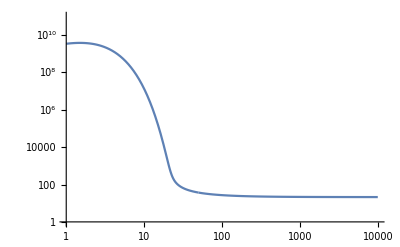

```mathematica
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,50},PlotRange->{{1,10000},{1,10^11}}];
LogLogPlot[Evaluate[y[x]/.solution2],{x,50,10000},PlotRange->{{1,10000},{1,10^11}}];
Show[%,%%]
```

```mathematica
LogLogPlot[{0.0384 Subscript[M,Pl] m Sigma x^(3/2) E^-x/.MyAssumptions,0},{x,1,1000},PlotRange->{{1,10000},{1,10^11}},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]},AxesLabel->{x,y},PlotLegends->Placed[{Subscript[y,eq], y},Below]];
Rasterize[Show[%,%%],ImageResolution->200]
```

-Graphics-

```mathematica
GN=6.707*10^(-39) GeV^(-2)
H0=2.131*10^(-42)GeV h
mChi=mC GeV
sigma = Sigma GeV^(-2)
s0=2890*(1.98*10^(-14) GeV)^3
```

(6.707×10^-39)/GeV^2

2.131×10^-42 GeV h

GeV mC

Sigma/GeV^2

2.24333×10^-38 GeV^3

```mathematica
Omega=((Sqrt[8 Pi GN]s0 21.3 8 Pi GN)/(1.32 * 10  sigma * 3 H0^2))//Simplify
```

(1.83892×10^-10 √(1/GeV^2) GeV)/(h^2 Sigma)

```mathematica
Omega/.{Sigma->10^(-10),GeV->1.}//Simplify
```

1.83892/h^2

```mathematica
Sigma*(1.98*10^(-14))^2/.{Sigma->10^(-10)}
```

3.9204×10^-38

```mathematica
Inverse[{{1,-v},{0,1}}]
```

{{1,v},{0,1}}

```mathematica
int=LoopIntegrate[Spur[l.γ+M 𝟙,(l-p).γ+M 𝟙],l,-p,M,M]
```

4 PVA[0,M]+(8 M^2-2 p.p) PVB[0,0,p.p,M,M]

```mathematica
sol=LoopRefine[int]//DiscExpand;
sol//FullSimplify
sol=sol/.{p.p->30^2}//Simplify
sol=sol/.{µ^2->30^2}//Simplify
solN =sol/.{M->163}//Simplify//N
(0.93^2*solN/(16 Pi^2))//Simplify
```

20 M^2-4 p.p+2 (6 M^2-p.p) (1/ϵ+Log[µ^2/M^2])+(2 (4 M^2-p.p) √(p.p (-4 M^2+p.p)) Log[(2 M^2-p.p+√(p.p (-4 M^2+p.p)))/(2 M^2)])/(p.p)

20 (-180+M^2)-8/15 (225-M^2)^(3/2) Log[(-450+M^2+30 √(225-M^2))/M^2]+12 (-150+M^2) (1/ϵ+Log[µ^2/M^2])

20 (-180+M^2)+12 (-150+M^2) (1/ϵ+Log[900/M^2])-8/15 (225-M^2)^(3/2) Log[(-450+M^2+30 √(225-M^2))/M^2]

(107470.-2.21534×10^-10 ⅈ)+317028. (-3.38511+1/ϵ)

(-5289.2-1.21335×10^-12 ⅈ)+1736.38/ϵ

```mathematica
Integrate[(M^2-p^2x(1-x))Log[(M^2-p^2x(1-x))/(mu^2)],{x,0,1}]
```

```mathematica
int1=LoopIntegrate[Subscript[𝕘, μ,ν](k.k+p1.k+M^2),k,-p1,M,M]
```

𝕘_(μ,ν) (PVA[0,M]+(2 M^2+(p1.p1)/2) PVB[0,0,p1.p1,M,M])

```mathematica
sol1=LoopRefine[int1]//DiscExpand;
```

```mathematica
sol1=sol1/.{p1.p1->M^2}
```

(6 M^2+5/2 √3 √(-M^4) Log[(M^2+√3 √(-M^4))/(2 M^2)]+7/2 M^2 (1/ϵ+Log[µ^2/M^2])) 𝕘_(μ,ν)

```mathematica
total=sol+sol1//Simplify
```

1/36 (2 (1+6/ϵ+6 Log[µ^2/M^2]) p1_μ p1_ν+(99 √3 √(-M^4) Log[1/2 (1+(√3 √(-M^4))/M^2)]+M^2 (250+141/ϵ+141 Log[µ^2/M^2])) 𝕘_(μ,ν))

```mathematica
Series[total,{M,0,2}]
```

1/18 (1+6/ϵ-12 Log[M]+6 Log[µ^2]) p1_μ p1_ν+1/36 (250-33 √3 π+141/ϵ-282 Log[M]+141 Log[µ^2]) 𝕘_(μ,ν) M^2+O[M]^3

```mathematica
Spur[l.γ+M 𝟙,(l-p).γ+M 𝟙]
```

4 M^2+4 l.l-4 l.p

```mathematica
0.93^2*(24 Pi^2)^(-1)(6*163^2-125^2)
```

525.026

```mathematica
gram= 5.62*10^(23) GeV
pb = 10^(-9)/0.389 GeV^(-2)
mb=10^(9)pb

cm=1/(1.98*10^(-14)) GeV^(-1)
```

5.62×10^23 GeV

(2.57069×10^-9)/GeV^2

2.57069/GeV^2

(5.05051×10^13)/GeV

```mathematica
1cm^2/gram
```

4538.72/GeV^3

```mathematica
500mb/(1 GeV)
```

1285.35/GeV^3

```mathematica
10^(-23) cm^2/GeV
```

25507.6/GeV^3

```mathematica
Eigenvalues[{{0,g1,g2},{g1,0,0},{g2,0,0}}]
{{0,g1,g2},{g1,0,0},{g2,0,0}}.Eigenvectors[{{0,g1,g2},{g1,0,0},{g2,0,0}}]
Eigenvalues[{{0,g1,0},{g1,0,0},{0,0,0}}]
```

{0,-√(g1^2+g2^2),√(g1^2+g2^2)}

{{0,g1,g2},{g1,0,0},{g2,0,0}}.{{0,-g2/g1,1},{-(√(g1^2+g2^2))/g2,g1/g2,1},{(√(g1^2+g2^2))/g2,g1/g2,1}}

{-g1,g1,0}

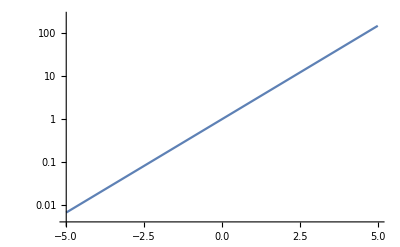

```mathematica
cdm[x_]:=E^(-x)
LogPlot[cdm[x],{x,-5,5}]
```

```mathematica
intF=LoopIntegrate[Spur[DiracMatrix[Subscript[γ, μ],(l-p).γ,Subscript[γ, ν],l.γ]],l,-p,0,0]
```

p_μ p_ν (8 PVB[0,1,p.p,0,0]+8 PVB[0,2,p.p,0,0])+𝕘_(μ,ν) (-4 PVA[0,0]+2 p.p PVB[0,0,p.p,0,0]+8 PVB[1,0,p.p,0,0])

```mathematica
intFref=LoopRefine[intF]
```

(-20/9-4/3 (1/ϵ+Log[-µ^2/(p.p)])) p_μ p_ν+((20 p.p)/9+4/3 p.p (1/ϵ+Log[-µ^2/(p.p)])) 𝕘_(μ,ν)

```mathematica
Spur[DiracMatrix[Subscript[γ, μ],(l-p).γ,Subscript[γ, ν],l.γ]]
```

8 l_μ l_ν-4 l_ν p_μ-4 l_μ p_ν-4 l.l 𝕘_(μ,ν)+4 l.p 𝕘_(μ,ν)

```mathematica
tensor=(Subscript[𝕘, μ,α] Subscript[(p+l), ρ]+Subscript[𝕘, α,ρ] Subscript[(p-2l), μ]+Subscript[𝕘, ρ,μ] Subscript[(l-2p), α])(Subscript[𝕘, ν,β] Subscript[(p+l), ω]-Subscript[𝕘, β,ω] Subscript[(2l-p), ν]-Subscript[𝕘, ω,ν] Subscript[(2p-l), β])Subscript[𝕘, α,β] Subscript[𝕘, ρ,ω]
tensoralt=(Subscript[𝕘, μ,α] Subscript[(p-l), ρ]+Subscript[𝕘, α,ρ] Subscript[(p), μ]+Subscript[𝕘, ρ,μ] Subscript[(l-2p), α])(Subscript[𝕘, ν,ω] Subscript[(2p-l), β]-Subscript[𝕘, ω,β] Subscript[(p), ν]+Subscript[𝕘, β,ν] Subscript[(l-p), ω])Subscript[𝕘, α,β] Subscript[𝕘, ρ,ω]
int3=LoopIntegrate[tensor,l,-p,0,0]
```

𝕘_(α,β) ((l_ρ+p_ρ) 𝕘_(α,μ)+(-2 l_μ+p_μ) 𝕘_(α,ρ)+(l_α-2 p_α) 𝕘_(μ,ρ)) ((l_ω+p_ω) 𝕘_(β,ν)-(2 l_ν-p_ν) 𝕘_(β,ω)-(-l_β+2 p_β) 𝕘_(ν,ω)) 𝕘_(ρ,ω)

𝕘_(α,β) ((-l_ρ+p_ρ) 𝕘_(α,μ)+p_μ 𝕘_(α,ρ)+(l_α-2 p_α) 𝕘_(μ,ρ)) ((l_ω-p_ω) 𝕘_(β,ν)-p_ν 𝕘_(β,ω)+(-l_β+2 p_β) 𝕘_(ν,ω)) 𝕘_(ρ,ω)

p_μ p_ν ((-6+𝒹) PVB[0,0,p.p,0,0]+(-6+4 𝒹) PVB[0,1,p.p,0,0]+(-6+4 𝒹) PVB[0,2,p.p,0,0])+𝕘_(μ,ν) (2 PVA[0,0]+4 p.p PVB[0,0,p.p,0,0]+(-6+4 𝒹) PVB[1,0,p.p,0,0])

```mathematica
int3ref=LoopRefine[int3]
```

(-67/9-11/3 (1/ϵ+Log[-µ^2/(p.p)])) p_μ p_ν+((58 p.p)/9+19/6 p.p (1/ϵ+Log[-µ^2/(p.p)])) 𝕘_(μ,ν)

```mathematica
intgh=LoopIntegrate[Subscript[(l-p), ν] Subscript[l, μ],l,-p,0,0]
```

p_μ p_ν (PVB[0,1,p.p,0,0]+PVB[0,2,p.p,0,0])+𝕘_(μ,ν) PVB[1,0,p.p,0,0]

```mathematica
intghref=LoopRefine[intgh]
```

(-5/18+1/6 (-1/ϵ-Log[-µ^2/(p.p)])) p_μ p_ν+(-(2 p.p)/9-1/12 p.p (1/ϵ+Log[-µ^2/(p.p)])) 𝕘_(μ,ν)

```mathematica
int3ref/2 - intghref//Simplify
```

-1/9 (31+15/ϵ+15 Log[-µ^2/(p.p)]) (p_μ p_ν-p.p 𝕘_(μ,ν))

```mathematica
int4=LoopIntegrate[1,l,0]
```

PVA[0,0]

```mathematica
int4ref=LoopRefine[int4]
```

0

```mathematica
intF2=LoopIntegrate[DiracMatrix[Subscript[γ, μ],l.γ,Subscript[γ, μ]],l,-p,0,0]
```

DiracMatrix[p.γ] (-2 PVB[0,1,p.p,0,0]+𝒹 PVB[0,1,p.p,0,0])

```mathematica
intF2ref=LoopRefine[intF2]
```

DiracMatrix[p.γ] (-1-1/ϵ-Log[-µ^2/(p.p)])

```mathematica
(*intG1=LoopIntegrate[DiracMatrix[Subscript[γ, ν],(q-l).γ,Subscript[γ, μ],(-p-l+q).γ,Subscript[γ, ν]],l,-q,p-q,0,0,0]*)
intG1=LoopIntegrate[DiracMatrix[Subscript[γ, ν],(-l).γ,Subscript[γ, μ],(-p-l).γ,Subscript[γ, ν]],l,0,p,0,0,0]
```

DiracMatrix[p.γ] p_μ (4 PVC[0,1,0,p.p,p.p,0,0,0,0]-2 𝒹 PVC[0,1,0,p.p,p.p,0,0,0,0]+4 PVC[0,2,0,p.p,p.p,0,0,0,0]-2 𝒹 PVC[0,2,0,p.p,p.p,0,0,0,0])+DiracMatrix[γ_μ] (-2 p.p PVC[0,1,0,p.p,p.p,0,0,0,0]+𝒹 p.p PVC[0,1,0,p.p,p.p,0,0,0,0]+4 PVC[1,0,0,0,p.p,p.p,0,0,0]-2 𝒹 PVC[1,0,0,0,p.p,p.p,0,0,0]-2 (p.p PVC[0,2,0,p.p,p.p,0,0,0,0]+𝒹 PVC[1,0,0,0,p.p,p.p,0,0,0])+𝒹 (p.p PVC[0,2,0,p.p,p.p,0,0,0,0]+𝒹 PVC[1,0,0,0,p.p,p.p,0,0,0]))

```mathematica
intG1ref=LoopRefine[intG1]
```

DiracMatrix[γ_μ] (-1+1/ϵ+Log[-µ^2/(p.p)])+(2 DiracMatrix[p.γ] p_μ)/(p.p)

```mathematica
intG2=LoopIntegrate[DiracMatrix[Subscript[γ, ρ],l.γ,Subscript[γ, ν]](Subscript[𝕘, μ,ν] Subscript[(2p+l), ρ]+Subscript[𝕘, ν,ρ] Subscript[(-p-2l), μ]+Subscript[𝕘, ρ,μ] Subscript[(l-p), ν]),l,0,p,0,0,0]
```

DiracMatrix[p.γ] p_μ (-2 PVC[0,1,0,p.p,p.p,0,0,0,0]+𝒹 PVC[0,1,0,p.p,p.p,0,0,0,0]-4 PVC[0,2,0,p.p,p.p,0,0,0,0]+2 𝒹 PVC[0,2,0,p.p,p.p,0,0,0,0])+DiracMatrix[γ_μ] (p.p PVC[0,1,0,p.p,p.p,0,0,0,0]+2 p.p PVC[0,2,0,p.p,p.p,0,0,0,0]-4 PVC[1,0,0,0,p.p,p.p,0,0,0]+4 𝒹 PVC[1,0,0,0,p.p,p.p,0,0,0])

```mathematica
intG2ref=LoopRefine[intG2]
```

DiracMatrix[γ_μ] (4+3 (1/ϵ+Log[-µ^2/(p.p)]))

```mathematica
Rasterize[Show[ParametricPlot[(1/2){Cos[t],Sin[t]+1},{t,0,2Pi},AxesLabel->{"Re a_j(s)","Im a_j(s)"},PlotLegends->Placed[{"Im a_j(s) = |a_j(s)|^2"},Below],PlotRange->{{-0.6,0.8},{-0.2,1.0}}],Graphics[Text["Tree level",{0.62,0.04}]],Graphics[{PointSize[0.025],Red,Point[{0.5,0.0}]}],Graphics[Text["All orders",{0.53,0.2}]],Graphics[{PointSize[0.025],Green,Point[{0.4,0.2}]}]],ImageResolution->300]
```

-Graphics-

```mathematica
DotProd[a_,b_]:=(a[[1,1]]*b[[1,1]]-Sum[a[[1,i]]*b[[1,i]],{i,2,4}]);
replace={Subscript[ϵ1, μ]->(1/mw)Subscript[p1, μ]+((2mw)/(t-2mw^2))Subscript[p3, μ],Subscript[ϵ2, μ]->(1/mw)Subscript[p2, μ]+((2mw)/(t-2mw^2))Subscript[p4, μ],
                Subscript[ϵ3, μ]->(1/mw)Subscript[p3, μ]+((2mw)/(t-2mw^2))Subscript[p1, μ],Subscript[ϵ4, μ]->(1/mw)Subscript[p4, μ]+((2mw)/(t-2mw^2))Subscript[p2, μ]};
replaceEps={ϵ[1]->(1/mw)k[1]+((2mw)/(t-2mw^2))k[3],ϵ[2]->(1/mw)k[2]+((2mw)/(t-2mw^2))k[4],
                ϵ[3]->(1/mw)k[3]+((2mw)/(t-2mw^2))k[1],ϵ[4]->(1/mw)k[4]+((2mw)/(t-2mw^2))k[2]};
epsilons=
{ϵ1.ϵ2->Contract[Subscript[ϵ1, μ] Subscript[ϵ2, μ]/.replace],ϵ1.ϵ3->Contract[Subscript[ϵ1, μ] Subscript[ϵ3, μ]/.replace],ϵ1.ϵ4->Contract[Subscript[ϵ1, μ] Subscript[ϵ4, μ]/.replace],
ϵ2.ϵ3->Contract[Subscript[ϵ2, μ] Subscript[ϵ3, μ]/.replace],ϵ2.ϵ4->Contract[Subscript[ϵ2, μ] Subscript[ϵ4, μ]/.replace],ϵ3.ϵ4->Contract[Subscript[ϵ3, μ] Subscript[ϵ4, μ]/.replace],
p1.ϵ2->Contract[Subscript[p1, μ] Subscript[ϵ2, μ]/.replace],p1.ϵ3->Contract[Subscript[p1, μ] Subscript[ϵ3, μ]/.replace],p1.ϵ4->Contract[Subscript[p1, μ] Subscript[ϵ4, μ]/.replace],
p2.ϵ1->Contract[Subscript[p2, μ] Subscript[ϵ1, μ]/.replace],p2.ϵ3->Contract[Subscript[p2, μ] Subscript[ϵ3, μ]/.replace],p2.ϵ4->Contract[Subscript[p2, μ] Subscript[ϵ4, μ]/.replace],
p3.ϵ1->Contract[Subscript[p3, μ] Subscript[ϵ1, μ]/.replace],p3.ϵ2->Contract[Subscript[p3, μ] Subscript[ϵ2, μ]/.replace],p3.ϵ4->Contract[Subscript[p3, μ] Subscript[ϵ4, μ]/.replace],
p4.ϵ1->Contract[Subscript[p4, μ] Subscript[ϵ1, μ]/.replace],p4.ϵ2->Contract[Subscript[p4, μ] Subscript[ϵ2, μ]/.replace],p4.ϵ3->Contract[Subscript[p4, μ] Subscript[ϵ3, μ]/.replace]};
standardReplace={ϵ1.p1->0,ϵ2.p2->0,ϵ3.p3->0,ϵ4.p4->0,p1.p1->mw^2,p2.p2->mw^2,p3.p3->mw^2,p4.p4->mw^2,p1.p2->(s-2mw^2)/2,p3.p4->(s-2mw^2)/2,p1.p3->(t-2mw^2)/2,p2.p4->(t-2mw^2)/2,p1.p4->(u-2mw^2)/2,p2.p3->(u-2mw^2)/2};
normalisation=Sqrt[Contract[Subscript[ϵ3, μ] Subscript[ϵ3, μ]/.replace]/.standardReplace]^(-1)
```

1/(√(3+(4 mw^4)/((-2 mw^2+t)^2)))

```mathematica
Clear[p,p1,p2,p3,p4]
tensor1= -Subscript[ϵ1, μ] Subscript[ϵ2, ν] Subscript[ϵ3, α] Subscript[ϵ4, β](-Subscript[𝕘, λ,κ]+(1/mw^2)Subscript[k, λ] Subscript[k, κ])(-Subscript[𝕘, μ,ν] Subscript[(p2-p1), λ]+Subscript[𝕘, ν,λ] Subscript[(p2+k), μ]-Subscript[𝕘, λ,μ] Subscript[(k+p1), ν])( Subscript[𝕘, α,β] Subscript[(p4-p3), κ]-Subscript[𝕘, β,κ] Subscript[(p4-k), α]-Subscript[𝕘, κ,α] Subscript[(k-p3), β] )/.{k->p1+p2};
(*tensor2=Subscript[ϵ1, μ] Subscript[ϵ2, ν] Subscript[ϵ3, α] Subscript[ϵ4, β](-Subscript[𝕘, λ,κ]+(1/mw^2)Subscript[k, λ] Subscript[k, κ])(-Subscript[𝕘, μ,ν] Subscript[(p4-p1), λ]+Subscript[𝕘, ν,λ] Subscript[(p4+k), μ]-Subscript[𝕘, λ,μ] Subscript[(k+p1), ν])( -Subscript[𝕘, α,β] Subscript[(p2-p3), κ]-Subscript[𝕘, β,κ] Subscript[(-p2+k), α]-Subscript[𝕘, κ,α] Subscript[(-k+p3), β] )/.{k->p1+p4};*)
tensor2=Subscript[ϵ1, μ] Subscript[ϵ2, ν] Subscript[ϵ3, α] Subscript[ϵ4, β](-Subscript[𝕘, λ,κ]+(1/mw^2)Subscript[k, λ] Subscript[k, κ])(Subscript[𝕘, μ,β] Subscript[(p1-p4), κ]+Subscript[𝕘, β,κ] Subscript[(p4-k), μ]+Subscript[𝕘, κ,μ] Subscript[(k-p1), β])( Subscript[𝕘, α,ν] Subscript[(p3-p2), λ]+Subscript[𝕘, ν,λ] Subscript[(p2+k), α]+Subscript[𝕘, λ,α] Subscript[(-k-p3), ν] )/.{k->-p1-p4};
tensor3=Subscript[ϵ1, μ] Subscript[ϵ2, ν] Subscript[ϵ3, α] Subscript[ϵ4, β](Subscript[𝕘, μ,ν] Subscript[𝕘, α,β]+Subscript[𝕘, μ,β] Subscript[𝕘, ν,α]-2 Subscript[𝕘, μ,α] Subscript[𝕘, ν,β]);
tensor4=-Subscript[ϵ1, μ] Subscript[ϵ2, ν] Subscript[ϵ3, α] Subscript[ϵ4, β](Subscript[𝕘, α,μ] Subscript[𝕘, β,ν]);
```

```mathematica
(*tensorOld=tensor/.epsilons/.{p1.p1->mw^2,p2.p2->mz^2,p3.p3->mw^2,p4.p4->mz^2}//Simplify;
tensorOld=tensorOld/.{p1.p2->(s-mw^2-mz^2)/2,p1.p3->-(s-2mw^2)/2,p1.p4->-(u-mw^2-mz^2)/2,p2.p3->-(u-mw^2-mz^2)/2,p2.p4->(2mz^2-t)/2,p3.p4->(s-mw^2-mz^2)/2}//Simplify;*)
```

```mathematica
(*massesOld={p1.p1->mw^2,p2.p2->mz^2,p3.p3->mw^2,p4.p4->mz^2,p1.p2->(1/2)(s-mw^2-mz^2),p1.p3->-(1/2)(s-2mw^2),p1.p4->-(1/2)(u-mw^2-mz^2),p2.p3->-(1/2)(u-mw^2-mz^2),p2.p4=(1/2)(2mz^2-t),p3.p4->(1/2)(s-mw^2-mz^2)};*)
```

```mathematica
tensor1=Contract[tensor1]/.standardReplace;
tensor2=Contract[tensor2]/.standardReplace;
tensor3=Contract[tensor3]/.standardReplace;
tensor4=Contract[tensor4]/.standardReplace;

(*masses={p1.p1->mw^2,p2.p2->mw^2,p3.p3->mw^2,p4.p4->mw^2,p1.p2->(1/2)(s-mw^2-mw^2),p1.p3->-(1/2)(s-2mw^2),p1.p4->-(1/2)(u-mw^2-mw^2),p2.p3->-(1/2)(u-mw^2-mw^2),p2.p4->(1/2)(2mw^2-t),p3.p4->(1/2)(s-mw^2-mw^2)};*)
```

```mathematica
(*replacements={p1.p2->e^2+p^2,p1.p3->-e^2-p^2 Cos[t],p1.p4->-e^2+p^2Cos[t],p2.p3->-e^2+p^2 Cos[t],p2.p4->e^2-p^2 Cos[t],p3.p4-> e^2 +p^2,
p1.ϵ2-> 2e p/mw,p1.ϵ3->(e p + e p Cos[t])/mw,p1.ϵ4->(e p - e p Cos[t])/mw,p2.ϵ3->(e p - e p Cos[t])/mw,p2.ϵ4->(e p + e p Cos[t])/mw,p3.ϵ4->(-2e p )/mw,ϵ1.ϵ2->(e^2+p^2)/mw^2,ϵ1.ϵ3->(p^2+e^2 Cos[t])/mw^2,ϵ1.ϵ4->(p^2-e^2 Cos[t])/mw^2,ϵ2.ϵ3->(p^2-e^2Cos[t])/mw^2,ϵ2.ϵ4->(p^2+e^2Cos[t])/mw^2,ϵ3.ϵ4->(p^2+e^2)/mw^2,p2.ϵ1->2 e p/mw,p3.ϵ1->(-e p - e p Cos[t])/mw,p3.ϵ2->(-e p+e p Cos[t])/mw,p4.ϵ1->(-e p + e p Cos[t])/mw,p4.ϵ2->(-e p - e p Cos[t])/mw,p4.ϵ3->-2e p/mw};*)
```

```mathematica
tensor1Expanded=(1/(s-mw^2))tensor1/.epsilons/.standardReplace//Simplify
tensor2Expanded=(1/(u-mw^2))tensor2/.epsilons/.standardReplace//Simplify
tensor3Expanded=tensor3/.epsilons/.standardReplace//Simplify
tensor4Expanded=((mw^2)/(t-mh^2))tensor4/.epsilons/.standardReplace//Simplify
(*tensorMasses=tensorNew/.masses//Simplify;*)
```

1/(4 (mw^2-s) (-2 mw^3+mw t)^4)(-512 mw^12 (s+2 t-u)+s t^4 (-t^2+u^2)+128 mw^10 (s^2+9 s t+9 t^2-2 s u-5 t u+u^2)-16 mw^6 t (3 s^3-10 t^3+s^2 (t-7 u)+5 t^2 u+4 t u^2-u^3-5 s (5 t^2+t u-u^2))-2 mw^2 t^3 (s^3-t^3+t u^2-2 s^2 (t+2 u)+3 s (-2 t^2+t u+u^2))+32 mw^8 (-19 t^3+2 s^2 (t-u)+9 t^2 u+4 t u^2-2 u^3+s (-27 t^2-6 t u+4 u^2))+4 mw^4 t^2 (6 s^3-s^2 (7 t+12 u)+3 t (-2 t^2+t u+u^2)+s (-22 t^2+2 t u+6 u^2)))

1/(4 (-2 mw^3+mw t)^4 (mw^2-u))(512 mw^12 (s-2 t-u)+t^4 (s^2-t^2) u+128 mw^10 (s^2-5 s t+9 t^2-2 s u+9 t u+u^2)-2 mw^2 t^3 (-t^3-6 t^2 u+s (3 t-4 u) u-2 t u^2+u^3+s^2 (t+3 u))+4 mw^4 t^2 (-6 t^3-22 t^2 u-7 t u^2+6 u^3+3 s^2 (t+2 u)+s (3 t^2+2 t u-12 u^2))-32 mw^8 (2 s^3-4 s^2 (t+u)+t (19 t^2+27 t u-2 u^2)+s (-9 t^2+6 t u+2 u^2))+16 mw^6 t (s^3+10 t^3+25 t^2 u-t u^2-3 u^3-s^2 (4 t+5 u)+s (-5 t^2+5 t u+7 u^2)))

1/4 (-8 (-1+t/(2 mw^2)+(6 mw^2)/(-2 mw^2+t))^2+((s t^2-2 mw^2 t (2 s+t-2 u)+8 mw^4 (s-u))^2)/((-2 mw^3+mw t)^4)+((8 mw^4 (s-u)-t^2 u+2 mw^2 t (-2 s+t+2 u))^2)/((-2 mw^3+mw t)^4))

((16 mw^4-4 mw^2 t+t^2)^2)/(4 (mh^2-t) (-2 mw^3+mw t)^2)

```mathematica
expr1=FullSimplify[Series[tensor1Expanded,{mw,0,0}],s+t+u==4mw^2]//Normal
expr2=FullSimplify[Series[tensor2Expanded,{mw,0,0}],s+t+u==4mw^2]//Normal
expr3=FullSimplify[Series[tensor3Expanded,{mw,0,0}],s+t+u==4mw^2]//Normal
expr4=FullSimplify[Series[tensor4Expanded,{mw,0,0}],s+t+u==4mw^2]//Normal
```

((t-u) (t+u))/(4 mw^4)-(-2 s^3+t^3-t u^2+4 s^2 (t+2 u)+2 s (2 t^2-3 t u+u^2))/(4 mw^2 s t)+(-8 s^4-t^4+t^2 u^2-2 s^3 (t+8 u)+4 s^2 (7 t^2+8 t u-4 u^2)+2 s t (2 t^2-3 t u+u^2))/(4 s^2 t^2)

(-s^2+t^2)/(4 mw^4)+((s-t) t (s+t)-2 (s-2 t) (s-t) u-4 (2 s+t) u^2+2 u^3)/(4 mw^2 t u)+((s-t) t^2 (s+t)+2 t (-s+t) (-s+2 t) u+4 (-4 s^2+8 s t+7 t^2) u^2-2 (8 s+t) u^3-8 u^4)/(4 t^2 u^2)

(s^2-2 t^2+u^2)/(4 mw^4)+(6 s^2-8 s t-12 t^2+8 s u-8 t u+6 u^2)/t^2+(2 t-u+s (-1+(4 u)/t))/mw^2

-t/(mh^2-t)+t^2/(mw^2 (4 mh^2-4 t))

```mathematica
Series[FullSimplify[Series[expr1+expr2+expr3+5*expr4,{mw,0,2}]//Normal,s+t+u==4mw^2],{mh,0,2}]
```

(s^4 t-s^2 t^3+2 s^4 u-2 s^3 t u-2 s^3 u^2+16 s^2 t u^2-t^3 u^2-2 s^2 u^3-2 s t u^3+2 s u^4+t u^4)/(4 s^2 t u^2)+(5 (s+u) mh^2)/(t (s+t+u))+O[mh]^3

```mathematica
(*tensorFull=FullSimplify[tensorMasses,4mw^2==s+t+u]*)
```

```mathematica
pk=Sqrt[e^2-mw^2];
k1={{e,0,0,pk}};
k2={{e,0,0,-pk}};
k3={{-e,0,-pk Sin[theta],-pk Cos[theta]}};
k4={{-e,0,pk Sin[theta],pk Cos[theta]}};
normalisation=1/9*1/(32 Pi);
```

```mathematica
integratedOverEnergy[f_,energy_,higgsmass_]:=1/2 NIntegrate[f/.{e->energy,mh->higgsmass},{theta,0.1,Pi-0.1}]
```

```mathematica
withoutHiggs=tensor1Expanded+tensor2Expanded+tensor3Expanded/.{s->DotProd[k1+k2,k1+k2],t->DotProd[k1+k3,k1+k3],u->DotProd[k1+k4,k1+k4]}/.{mw->80}//Simplify;
withHiggs=tensor1Expanded+tensor2Expanded+tensor3Expanded+5tensor4Expanded/.{s->DotProd[k1+k2,k1+k2],t->DotProd[k1+k3,k1+k3],u->DotProd[k1+k4,k1+k4]}/.{mw->80}//Simplify;
integratedWithoutHiggs={};
integratedWithHiggs={};
integratedWithHeavyHiggs={};
Do[AppendTo[integratedWithoutHiggs,{i*100, normalisation*integratedOverEnergy[withoutHiggs,i*50,125]}],{i,3,40}]
Do[AppendTo[integratedWithHiggs,{i*100, normalisation*integratedOverEnergy[withHiggs,i*50,125]}],{i,3,40}]
Do[AppendTo[integratedWithHeavyHiggs,{i*100, normalisation*integratedOverEnergy[withHiggs,i*50,3000]}],{i,3,40}]
```

```mathematica
withHiggs=tensor1Expanded+tensor2Expanded+tensor3Expanded+5tensor4Expanded/.{s->DotProd[k1+k2,k1+k2],t->DotProd[k1+k3,k1+k3],u->DotProd[k1+k4,k1+k4]}/.{ct->0,st->1,mw->80}//N;
```

```mathematica
line1=Line[{{1,1},{4000,1}}];
lineStyle={Thick,Red};
Rasterize[ListPlot[{Abs[integratedWithoutHiggs],Abs[integratedWithHiggs],Abs[integratedWithHeavyHiggs]},AxesLabel->{"E_CM [GeV]","|a_0|"},PlotLegends->Placed[{"No Higgs", "Higgs, m_h= 125 GeV", "Higgs, m_h= 3000 GeV"},Below],Epilog->{Directive[lineStyle],line1}],ImageResolution->200]
```

-Graphics-

```mathematica
?Rasterize
?ListPlot
```

Rasterize[g] returns a rasterized graphic of g. 
Rasterize[g,elem] gives the element elem associated with the rasterized form of g.

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

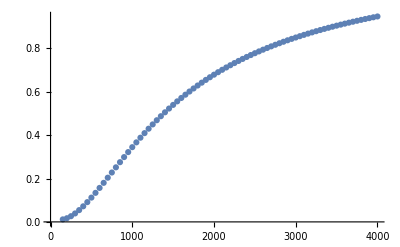

```mathematica
ListPlot[Abs[integratedWithHeavyHiggs]]
```